```mathematica
noteDir=NotebookDirectory[];
SetDirectory[noteDir];
<<BubbleSortDSA`
 
 (* Hides all In[] and Out[] CellLabels *)
SetOptions[$FrontEnd,ShowCellLabel->False]
```

Notebook[1]
 |  |  |  |

# Tutorial per l’algoritmo di ordinamento Bubble Sort per studenti con DSA

## Progetto didattico del corso di Matematica Computazionale dell’Università di Bologna A.A. 2019/2020

```mathematica
Hyperlink["Licenza Creative Commons Attribuzione 4.0 Internazionale","https://creativecommons.org/licenses/by/4.0/"]
```

[Licenza Creative Commons Attribuzione 4.0 Internazionale](https://creativecommons.org/licenses/by/4.0/)

## Contenuto del Notebook

Questo tutorial è rivolto ad una classe terza di un liceo scientifico ad indirizzo scienze applicate. Il suo obiettivo è l’apprendimento di un semplice algoritmo di ordinamento chiamato Bubble Sort. 

I prerequisiti richiesti per poter affrontare tale argomento e risolvere i problemi che saranno sottoposti  sono:

basi di programmazione strutturata

padronanza nell’uso delle strutture di controllo decisionali, iterative, nonché di strutture dati quali i vettori

conoscenza della programmazione imperativa

## ISTRUZIONI PER L’USO

“Evaluate Notebook” ?

Screenshot

## Indice

## Bubble Sort: intuizione

#### Gli algoritmi di ordinamento

Un algoritmo è un particolare programma che risolve una classe di problemi con una certa efficienza, generalmente espressa in termini di velocità di calcolo. 
Con algoritmo di ordinamento si intende una particolare classe di algoritmi che vengono usati per ordinare gli elementi di un vettore dal più piccolo al più grande - o viceversa. Esistono svariati algoritmi di ordinamento, ognuno dei quali adotta criteri e procedure diverse. Vedremo il funzionamento di uno dei più semplici, il Bubble Sort (detto anche ordinamento a bolla).

#### Il Bubble Sort

Il nome dell’algoritmo è legato al suo funzionamento: ad ogni passata l’elemento maggiore del vettore “galleggia” fino all’ultima posizione del vettore stesso.
Per ottenere questo ogni coppia di elementi adiacenti viene confrontata e invertita di posizione se gli elementi sono nell’ordine sbagliato. Per esempio, saranno confrontati il primo e il secondo elemento, poi il secondo e il terzo, poi il terzo e il quarto, e così via fino al confronto fra il penultimo e l’ultimo elemento. Questa operazione viene poi ripetuta per un numero di volte pari alla lunghezza del vettore meno 1. 
Se prendiamo come esempio il seguente vettore:

( 9  5  8  3  1 )

La prima coppia di elementi ad essere confrontata sarà 9 e 5. Siccome 9 > 5  viene effettuato il primo scambio:

( 5  9  8  3  1 )

La coppia successiva è 9 e 8. 9 > 8 quindi si effettua un altro scambio:

( 5  8  9  3  1 )

E così via fino ad aver confrontato tutte le coppie adiacenti. A questo punto il vettore apparirà così:

( 5  8  3  1  9 )

Dopo questa prima iterazione l’algoritmo ripete questi passaggi per altre 3 volte, per un totale di 4 iterazioni (pari alla lunghezza del vettore meno uno). Alla fine gli elementi del vettore appariranno nel giusto ordine.

#### Conigli e Tartarughe

Durante ogni iterazione almeno un valore viene spostato rapidamente fino a raggiungere la sua collocazione definitiva; in particolare, alla prima iterazione il numero più grande raggiunge l’ultima posizione dell’array, alla seconda il secondo numero più grande raggiunge la penultima posizione, e così via. La struttura dell’algoritmo quindi porta ad avere elementi che si spostano verso la posizione corretta più velocemente di altri. Questi elementi sono chiamati “conigli”.  Al contrario, gli elementi che si spostano verso la posizione corretta impiegando più tempo sono chiamati “tartarughe”.
Riprendendo l’esempio di prima, il vettore dopo la prima iterazione appare così:

( 5  8  3  1  9 )

A questo stato della computazione l’elemento 9 è il “coniglio”, poiché con una sola iterazione si è spostato verso la posizione corretta. L’elemento 1, così come gli altri, è una “tartaruga”: durante un’iterazione si è spostato di una sola posizione verso la posizione corretta.

### Guarda l’algoritmo in azione

```mathematica
BubbleSortAnimation[6, esecuzione]
```

## Bubblesort: pseudocodice

L’algoritmo può essere espresso in pseudocodice nel seguente modo:

```mathematica
CellPrint[Cell["procedure BubbleSort (A : lista degli elementi da ordinare)

	N = len (A)

	for ( i = 1; i < N; i++ )
	{
		for ( j = 0; j < N - 1; j++ )
		{
			if ( A[j] > A[j + 1] )
			{
				scambia A[j] e A[j + 1]
			}
    	}
	}","Text",
FontFamily->"Courier",
Background->GrayLevel[0.90]]]
```

procedure BubbleSort (A : lista degli elementi da ordinare)

	N = len (A)

	for ( i = 1; i < N; i++ )
	{
		for ( j = 0; j < N - 1; j++ )
		{
			if ( A[j] > A[j + 1] )
			{
				scambia A[j] e A[j + 1]
			}
    	}
	}

dove con la funzione “scambia” si fa riferimento ad una procedura che inverte la posizione di due elementi del vettore.

L’algoritmo prevede due cicli annidati. Il primo è un ciclo for che si esegue N-1 volte, dove N è uguale alla lunghezza del vettore A. Il secondo ciclo for confronta le coppie adiacenti, partendo dal primo elemento fino all’ultimo, e scambiando gli elementi se non sono ordinati.

### Domande di verifica

```mathematica
StartBubbleSortQuiz[]
```

## Mettiti alla prova!

Prova ad ordinare l’array, verificando ad ogni passo se lo scambio è corretto.

```mathematica
StartBubbleSortGame[]
```

## Bubblesort: complessità

L’efficienza di un algoritmo viene espressa con l’ordine di complessità. Generalmente la complessità dipende dal numero n di elementi del vettore. 
Quando le operazioni da fare per completare l’algoritmo sono proporzionali al numero di elementi del vettore l’ordine di complessità è indicato come O(n), che  si legge “O grande di n”.

Nel caso del Bubble Sort le cose vanno peggio di O(n) e i calcoli da farsi sono proporzionalia a n.b2, dunque l’ordine di complessità dell’algoritmo è O(n.b2).

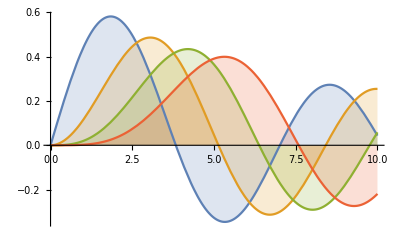

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

#### Esempio

Guarda come cambia la complessità al variare del numero di elementi di un array random!

```mathematica
Slider[Dynamic[x]]
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

-Graphics-

## Bubble Sort: versione ottimizzata

Se si osserva il comportamento del Bubble Sort si può notare una proprietà dell’algoritmo, particolarmente visibile nell’esempio dei conigli e delle tartarughe. 
Dopo la prima iterazione l’elemento più grande si troverà nell’ultima posizione della lista, la sua definitiva; alla seconda iterazione il secondo elemento più grande si troverà in penultima posizione, a sua volta definitiva, e così via. Sfruttando questa proprietà è possibile costruire una versione alternativa dell’algoritmo che effettua un numero di operazioni minore. Questo è possibile accorciando il numero di passi effettuati dal for più interno: ad ogni iterazione il ciclo può accorciarsi di un passo rispetto al precedente, evitando di scorrere la lista fino in fondo.

Possiamo rappresentare questa versione ottimizzata dell’algoritmo Bubble Sort con il seguente pseudocodice:

```mathematica
CellPrint[Cell["procedure BubbleSort (A : lista di elementi da ordinare)

	N = len (A)

	for ( i = 1; i < len (A); i++ )
	{
		for ( j = 0; j < N - 1; j++ )
		{
			if ( A[j] > A[j + 1] )
			{
				scambia A[j] e A[j + 1]
			}
		}
		N--                      // ad ogni passaggio si accorcia di uno il ciclo di for
	}
",
"Text",
FontFamily->"Courier",
Background->GrayLevel[0.90]]]
```

procedure BubbleSort (A : lista di elementi da ordinare)

	N = len (A)

	for ( i = 1; i < len (A); i++ )
	{
		for ( j = 0; j < N - 1; j++ )
		{
			if ( A[j] > A[j + 1] )
			{
				scambia A[j] e A[j + 1]
			}
		}
		N--                      // ad ogni passaggio si accorcia di uno il ciclo di for
	}

Dal momento che questo algoritmo esegue un numero di operazioni minore rispetto al Bubble Sort classico la sua complessità è inferiore.

```mathematica
BubbleSortAnimation[6, esecuzione]
```

## Riferimenti

[1] Sito web: https://it.wikipedia.org/wiki/Bubble_sort
[2] Sito web: https://algorithmist.com/wiki/Bubble_sort
[3] Sito web: https://docs.google.com/presentation/d/1WUItu5W5OM0zBuMj5JzuR1L_8p26dV66h_9M4RwQXWQ/edit#slide=id.g7455cc164d_1_0

## Note

Scoperte che abbiamo fatto ?